```mathematica
{NotebookFileName[],DateString[]}
```

{H:\morpheus\worm4\worm4.nb,Tue 16 Mar 2021 07:58:04}

## Setup

```mathematica
Needs["Developer`"]
```

```mathematica
$HistoryLength=5
```

5

```mathematica
curDir=FileNameDrop[NotebookFileName[]]
```

H:\morpheus\worm4

```mathematica
modelName=FileNameTake[curDir,-1]
```

worm4

```mathematica
logFile="logger.csv"
```

logger.csv

```mathematica
ksfdDir="D:\\WSL\\KSFD"
```

D:\WSL\KSFD

```mathematica
ksfdDataDir=FileNameJoin[{ksfdDir,"data"}]
```

D:\WSL\KSFD\data

```mathematica
FileNames["*",ksfdDataDir]
```

{D:\WSL\KSFD\data\energies138.mx,D:\WSL\KSFD\data\energies139.mx,D:\WSL\KSFD\data\energies140.mx,D:\WSL\KSFD\data\energies141.mx,D:\WSL\KSFD\data\energies157.mx,D:\WSL\KSFD\data\images103,D:\WSL\KSFD\data\images133,D:\WSL\KSFD\data\images134,D:\WSL\KSFD\data\images135,D:\WSL\KSFD\data\images136g,D:\WSL\KSFD\data\images136m,D:\WSL\KSFD\data\images90,D:\WSL\KSFD\data\images91,D:\WSL\KSFD\data\images92,D:\WSL\KSFD\data\images93,D:\WSL\KSFD\data\images94,D:\WSL\KSFD\data\images95,D:\WSL\KSFD\data\last133plot.png,D:\WSL\KSFD\data\last92plot.png,D:\WSL\KSFD\data\o103endPlot.pdf,D:\WSL\KSFD\data\o103step0Plot.pdf,D:\WSL\KSFD\data\o134nx128dtndterrs.csv,D:\WSL\KSFD\data\o134nx512dtndterrs.csv,D:\WSL\KSFD\data\o134nxndt1errs.csv,D:\WSL\KSFD\data\o135ampsPlot.pdf,D:\WSL\KSFD\data\o135step0Plot.pdf,D:\WSL\KSFD\data\o136gnx512dtnerrs.csv,D:\WSL\KSFD\data\o136gnxndt4errs.csv,D:\WSL\KSFD\data\o136mnx512dtnerrs.csv,D:\WSL\KSFD\data\o136mnxndt4errs.csv,D:\WSL\KSFD\data\o93nx512dtndterrs.csv,D:\WSL\KSFD\data\o93nxndt1errs.csv,D:\WSL\KSFD\data\o94ampsPlot.pdf,D:\WSL\KSFD\data\o94step0Plot.pdf,D:\WSL\KSFD\data\o95dterrs.csv,D:\WSL\KSFD\data\o95nx512dtnerrs.csv,D:\WSL\KSFD\data\o95nxerrs.csv,D:\WSL\KSFD\data\o95nxndt2errs.csv,D:\WSL\KSFD\data\options138,D:\WSL\KSFD\data\options139,D:\WSL\KSFD\data\options140,D:\WSL\KSFD\data\options141,D:\WSL\KSFD\data\options143_6,D:\WSL\KSFD\data\options157}

## Functions

```mathematica
sweepDir1=FileNameJoin[{curDir,modelName<>"a"}]
```

H:\morpheus\worm4\worm4a

```mathematica
sims1=FileNames["sim*",sweepDir1];
Short[sims1]
```

{H:\morpheus\worm4\worm4a\sim_0.0_0.0,«674»,H:\mo…8_8000}

```mathematica
sim1=Import[
FileNameJoin[{sims1⟦1⟧,logFile}],
{"CSV","Dataset"}
,HeaderLines->1
]
```

```mathematica
sim1⟦1⟧["MKtemp"]
```

0

```mathematica
sim1⟦1⟧//Keys
```

```mathematica
sim1[GroupBy["time"]]
```

```mathematica
sim1[GroupBy["time"]]⟦-1⟧[StandardDeviation]
```

```mathematica
MissingQ[ds1⟦1,"MKtime"⟧]
```

Part::partd: Part specification ds1⟦1,MKtime⟧ is longer than depth of object.

False

```mathematica
estimateVelocityDiffusion[
sweepDir_String,
logName_:logFile
]:=Module[{sweepds,tfinal,MKtime,temp,cms,μx,μy,σx,σy},
sweepds=Import[
FileNameJoin[{sweepDir,logName}],
{"CSV","Dataset"}
,HeaderLines->1
];
sweepds=sweepds[GroupBy["time"]]⟦-1⟧;
temp=sweepds⟦1⟧["MKtemp"];
cms=sweepds⟦1⟧["cmstrength"];
tfinal=sweepds⟦1⟧["time"];
MKtime=sweepds⟦1⟧["MKtime"];
If[FailureQ[MKtime]||MissingQ[MKtime],MKtime=tfinal/10000];
{σx,σy}=sweepds[All,{"delta_r.x","delta_r.y"}][StandardDeviation]/@{"delta_r.x","delta_r.y"};
{μx,μy}=sweepds[All,{"delta_r.x","delta_r.y"}][Mean]/@{"delta_r.x","delta_r.y"};
<|
"cmstrength"->cms,
"temperature"->temp,
"MKtime"->MKtime,
"cmtratio"->If[PossibleZeroQ[temp],∞,cms/temp],
"tfinal"->tfinal,
"vmean"->μx/tfinal,
"Dx"->σx^2/(2tfinal),
"Dy"->σy^2/(2tfinal),
"Dxy"->(σx^2+σy^2)/(4tfinal)
|>
]
```

```mathematica
estimateVelocityDiffusion[sims1⟦1⟧]
```

<|cmstrength→0,temperature→0,MKtime→1,cmtratio→∞,tfinal→10000,vmean→0.00004655,Dx→0.00498621,Dy→0.00497453,Dxy→0.00498037|>

## Plots

```mathematica
ds1=Dataset[estimateVelocityDiffusion/@sims1]
```

```mathematica
ds1[GroupBy["temperature"]]⟦-1⟧
```

```mathematica
{tfinal1,MKtime1}=ds1⟦1⟧/@{"tfinal","MKtime"}
```

{10000,1}

```mathematica
DeleteDuplicates@Flatten@Normal@Keys[ds1]
```

{cmstrength,temperature,MKtime,cmtratio,tfinal,vmean,Dx,Dy,Dxy}

```mathematica
Normal[ds1[GroupBy["cmstrength"]]⟦1,All,"temperature"⟧]//Sort//InputForm
```

{0, 0.2, 0.4, 0.6, 0.8, 1, 2, 
 4, 6, 8, 10, 20, 40, 60, 80, 
 100, 200, 400, 600, 800, 
 1000, 2000, 4000, 6000, 
 8000, 10000}

```mathematica
ds1[GroupBy["cmstrength"]]⟦1⟧[SortBy["temperature"]]
```

```mathematica
ds1[SortBy["cmstrength"]][GroupBy["cmstrength"]]
```

```mathematica
Clear[dsPlots];
dsPlots[
xname_String,
yname_String:"Dxy",
byname_String:"cmstrength",
dsin_Dataset:ds1
]:=Block[{is=400,dss,gds,temp,labels,data},
gds=dsin[SortBy[byname]][GroupBy[byname]];
gds=Normal[gds];
labels={};
data=Table[
temp=ds⟦1⟧[byname];
AppendTo[labels,temp];
Transpose@{
Normal[ds⟦All,xname⟧],
Normal[ds⟦All,yname⟧]
},
{ds,gds}
];
ListLogLinearPlot[data
,PlotRange->{Full,Full}
,PlotLegends->labels
,Joined->True
,Frame->{{True,True},{True,True}}
,FrameLabel->{{yname,None},{xname,None}}
,ImageSize->is
]
]
```

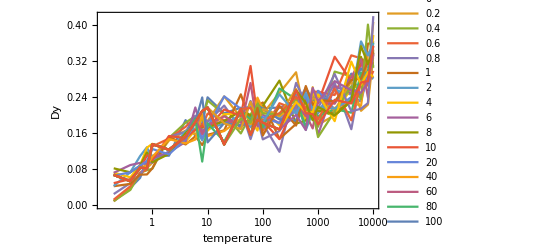

```mathematica
dsPlots["temperature","Dy"]
```

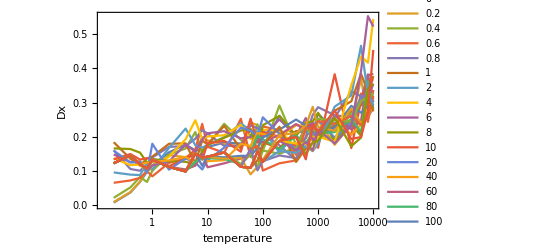

```mathematica
dsPlots["temperature","Dx"]
```

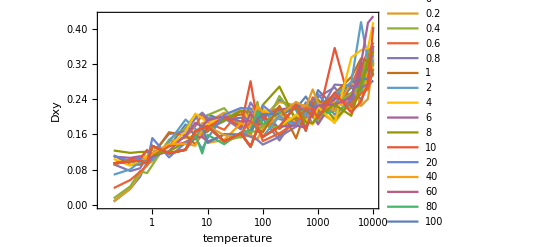

```mathematica
dsPlots["temperature","Dxy"]
```

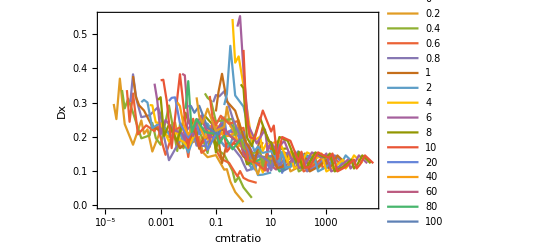

```mathematica
vplot2=dsPlots["cmtratio","Dx","cmstrength"];
Show[vplot2
,Frame->True
]
```

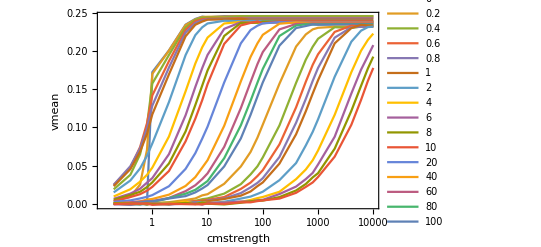

```mathematica
Show[
dsPlots["cmstrength","vmean","temperature"]
,Frame->True
]
```

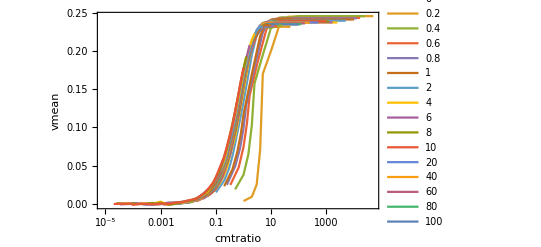

```mathematica
vplot2=dsPlots["cmtratio","vmean","temperature"];
Show[vplot2
,Frame->True
]
```

```mathematica
ds1[Select[#["temperature"]==10000&&#["cmstrength"]==10000&]]
```

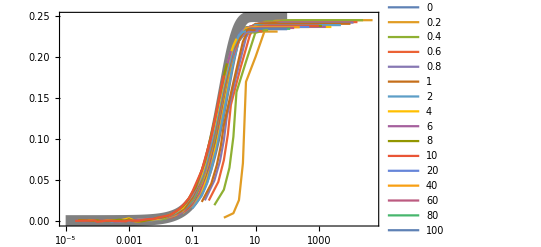

```mathematica
Show[
LogLinearPlot[(1-ⅇ^-x)/4,{x,10^-5,100}
,PlotStyle->{Thickness[0.02],Gray}
],
vplot2
,Frame->True
,PlotRange->All
]
```

OK, let’s try to understand this. Metropolis works like this. First, we have a set of possible steps we might take. What those steps are for the CPM is not clearly documented in the Morpheus doco anywhere that I can find. This is really the critical question. We then choose one from that set and calculate the ΔE for that step. If ΔE<0, we take the step. If ΔE>0, we calculate P=ⅇ^(-ΔE/T), then we take the step with probability P, meaning that we are unlikely to take steps that cause a big positive change in energy, big being assessed relative to the temperature. For chemotaxis, E=μF, where μ is a parameter, chemotaxis strength, and F is some spatially varying field.

Now, in these calibration runs I set up a field whose gradient is exactly ∇F=(F_x,F_y)=(1,0) in grid units. Then I varied μ and T. The first thing you can see from the above description is that the result should depend only on the ratio μ/T. Thus in some of the plots above I plotted diffusion or velocity vs cmtratio, which is μ/T. And if fact it more or less works. The curves more or less superimpose. This is more obvious for velocity. plots of v vs μ/T for different temperatures almost superimpose, except at T≤1. The plots of D_x vs μ/T are a lot noisier, but the curves for different μ match pretty well. (Actually, something simpler is true for D—D and D_y depend only on T to a good first approximation. D_x depends on on T except at T≤1, where μ makes a difference.) Something weird is going on at low T—I’m guessing that integer arithmetic is used in some part of the computation, so that there is truncation. 

Now, there are two limits where the results are sort of predictable. First, in the limit of very high T, every step should be taken. So the velocity should be low. And the diffusion should be maximal, and should correspond to 1/4⟨‖Δ x⃗‖^2⟩, where Δ x⃗ is the change in cell center position caused by a single step. This maxes out at about 0.3, although it is easy to imagine that it has not saturated even at T=10^4 and would go higher if I went to higher temps. I also noted when I ran the sims that it took a lot longer to run a sim at T=10^4 than at, say, T=10. This suggests that T also affects the sampling strategy, causing a larger sample to be tried.

The other simple limit in principle is μ/T→∞. This should cause every step that produces a move in the positive x direction to be accepted and every step in the negative x direction rejected. So the mean velocity should just be the mean size of a positive x step. This is consistently v≈0.25.

Suppose that Δx={-1,0,1} with probabilities {1/4,1/2,1/4}. And let’s suppose we always accept the positive step. We accept the negative step with probability ⅇ^(-μ/T). Then the predicted mean velocity is

v̄=1/4·1+1/2·0+1/4·ⅇ^(-υ/T)·(-1)
=1/4(1-ⅇ^(-υ/T))

In fact, that fits the v vs μ/T plot fairly well. The variance, though, ought to be

```mathematica
mdist=EmpiricalDistribution[{1/4,1/2+(1/4)(1-ⅇ^-μ),(1/4)ⅇ^-μ}->{1,0,-1}
]
```

DataDistribution[…]

```mathematica
Mean[mdist]//Simplify
```

1/4-ⅇ^-μ/4

```mathematica
Variance[mdist]//FullSimplify
```

1/8 ⅇ^-μ (3+Cosh[μ]+2 Sinh[μ])

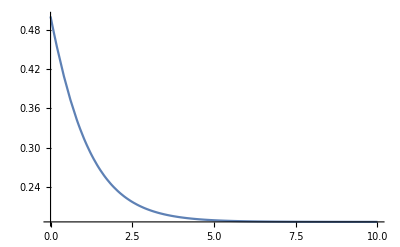

```mathematica
Plot[Variance[mdist],{μ,0,10}
,PlotRange->Full
]
```

So, the results mostly make sense. At every T, the maximum velocity, that attained when μ/T is large, approaches 1/4. Furthermore, the approach to this v_max is exponential—v=1/4(1-ⅇ^(-μ/T)) is a fairly good approximation at all but the lowest T.

This dependence is apparently well explained by a sample distribution that that includes steps of Δx∈{-1,0,1} with probabilities {1/4,1/2,1/4}. If you choose the positive option at every step where it is available, or 0 otherwise, you get a mean velocity of 1/4.

The puzzle, though, is the variance. This distribution has a variance of 1/2. That should lead to a maximum diffusion constant of 1/4. But the numbers are larger than that for high T.

```mathematica
ds1[Select[#["temperature"]==10000&]]⟦All,"Dxy"⟧
```

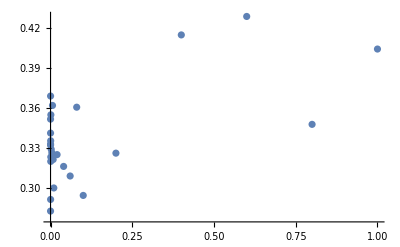

```mathematica
ListPlot[
ds1[Select[#["temperature"]==10000&]]⟦All,{"cmtratio","Dxy"}⟧
,PlotRange->All
]
```

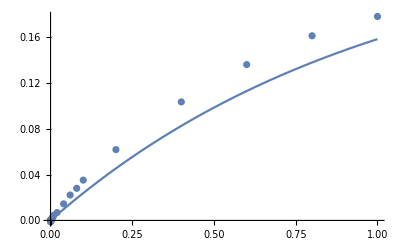

```mathematica
Show[
ListPlot[
ds1[Select[#["temperature"]==10000&]]⟦All,{"cmtratio","vmean"}⟧
,PlotRange->All
],
Plot[(1-ⅇ^-x)/4,{x,0,1}
]
]
```

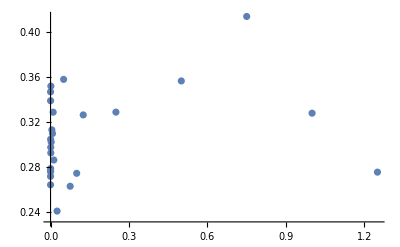

```mathematica
ListPlot[
ds1[Select[#["temperature"]==8000&]]⟦All,{"cmtratio","Dxy"}⟧
,PlotRange->All
]
```

Together, these numbers suggest that the sample changes as T increases, with the mean of the positive possibilities growing a bit larger than 1/4 and the variance growing, too.

I probably ought to do this calculation with a diagonal gradient to see if Δx and Δy are correlated, which could cause problems. But if that is true, I’m not sure what I could do with the information. I don’t have a way of making the chemotactic strength nonisotropic. So I guess I would just have to live with it.

## Simulation parameter values

Let’s suppose I set up a toy model with 360 worms on an 0.2×0.2 cm domain with a 75×75 grid.

```mathematica
width2=height2=Quantity[0.2,"Centimeters"];
nx2=ny2=75;
dt2=Quantity[0.15,"Seconds"];
{dx2,dy2}={width2,height2}/{nx2,ny2}
```

{0.00266667 cm,0.00266667 cm}

```mathematica
{wormwidth2,wormlength2}=Quantity[{15,240},"Micrometers"]
```

{15 µm,240 µm}

```mathematica
wormsize2=(wormwidth2 wormlength2)/(dx2 dy2)
```

5.0625

```mathematica
gridunitD2=(dx2 dy2)/Quantity[dt2,"Seconds"]
```

0.0000474074 cm^2/s^2

That’s what a diffusion constant of 1 in grid units would correspond to in cm^2 s^-1.

```mathematica
d139final=Import[
FileNames["*",FileNameJoin[{ksfdDataDir,"options139"}]]⟦-1⟧,
"Data"
];
i139final=d139final["/images"];
p139final=<|ImportString[d139final["/params"],"JSON"]|>
```

<|D_1_1→1/1000000,nligands_2→1,alpha_2→1500,alpha_1→1500,Umin→1/10000000,randgridnh→0,nwidth→384,variance_interval→100.,variance_timing_function→2002.03,s_1_1→0.01,tmax→200000.,ngroups→1,atol→0.01,randgridnw→0,CFL_safety_factor→0.5,dt→1/100000000,rhomin→1/10000000,lastvart→0.,s_2_1→0.001,ky0→2.,aUr→0.120891,kx0→3.4641,nligands_1→1,aUa→0.863036,maxsteps→10000,rhomax→28000,rtol→1/1000000,maxscale→2.,ndepth→384,dim→2,murho0→9000.,rho0→9000.,srho0→90.,D_2_1→1/100000,nheight→384,sigma→0.02357,series_1_1→1,cushion→2000,variance_rate→0.,t0→0.,k0→4.,lamda→0.000955351,gamma_2_1→0.001,slowdown→0.02,s2→5.55545×10^-6,beta_2→-0.0000111109,beta_1→0.0000111109,depth_1_1→0.4,gamma_1_1→0.01,conserve_worms→False,randgridnd→0,U0_1_1→,width→1,nelements→384,height→1,degree→3,depth→1.,weight_1_1→1.,Nworms→0,t→200203.|>

The following is our desired worm diffusion rate in real units.

```mathematica
σ139=Quantity[p139final["s2"],("Centimeters")^2/"Seconds"]
```

5.55545×10^-6 cm^2/s

In grid units, we need

```mathematica
σ139/gridunitD2
```

0.117185 s

```mathematica
p139final["D_1_1"]/(dx2 dy2)
```

0.140625 /cm^2

## worm4b

```mathematica
sweepDir2=FileNameJoin[{curDir,"worm4b2"}]
```

H:\morpheus\worm4\worm4b2

```mathematica
sims2=FileNames["sim*",sweepDir2];
Short[sims2]
```

{H:\morphe…m_0.0_0.0,«674»,…}

```mathematica
estimateVelocityDiffusion[sims2⟦-1⟧]
```

<|cmstrength→8,temperature→8000,MKtime→0.15,cmtratio→1/1000,tfinal→1500,vmean→0.0031493,Dx→1.48052,Dy→2.06624,Dxy→1.77338|>

```mathematica
ds2=Dataset[estimateVelocityDiffusion/@sims2]
```

```mathematica
{tfinal2,MKtime2}=ds2⟦1⟧/@{"tfinal","MKtime"}
```

{1500,0.15}

```mathematica
ds2[GroupBy["temperature"]]⟦-1⟧
```

```mathematica
DeleteDuplicates@Flatten@Normal@Keys[ds2]
```

{cmstrength,temperature,MKtime,cmtratio,tfinal,vmean,Dx,Dy,Dxy}

```mathematica
Normal[ds2[GroupBy["cmstrength"]]⟦1,All,"temperature"⟧]//Sort//InputForm
```

{0, 0.2, 0.4, 0.6, 0.8, 1, 2, 
 4, 6, 8, 10, 20, 40, 60, 80, 
 100, 200, 400, 600, 800, 
 1000, 2000, 4000, 6000, 
 8000, 10000}

```mathematica
ds2[GroupBy["cmstrength"]]⟦1⟧[SortBy["temperature"]]
```

```mathematica
ds2[SortBy["cmstrength"]][GroupBy["cmstrength"]]
```

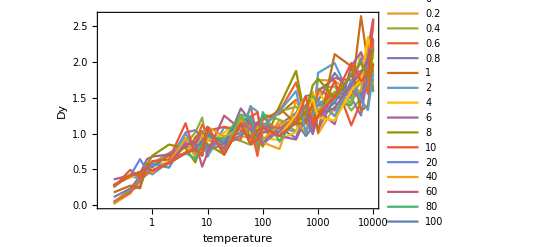

```mathematica
dsPlots["temperature","Dy","cmstrength",ds2]
```

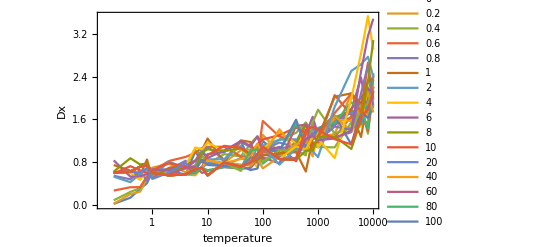

```mathematica
dsPlots["temperature","Dx","cmstrength",ds2]
```

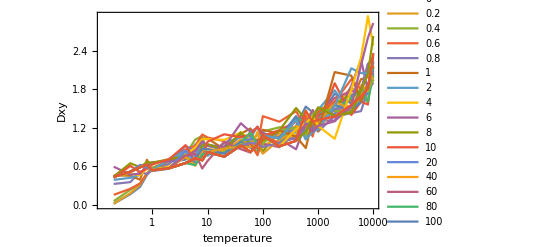

```mathematica
dsPlots["temperature","Dxy","cmstrength",ds2]
```

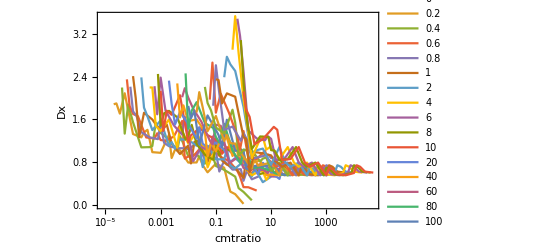

```mathematica
vplot2=dsPlots["cmtratio","Dx","cmstrength",ds2];
Show[vplot2
,Frame->True
]
```

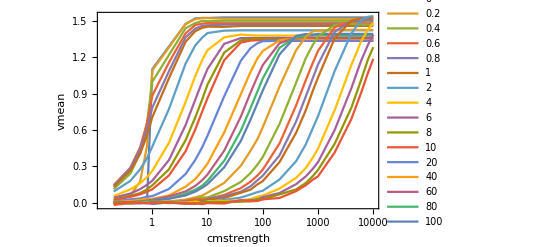

```mathematica
Show[
dsPlots["cmstrength","vmean","temperature",ds2]
,Frame->True
]
```

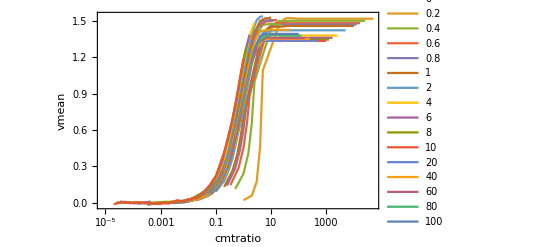

```mathematica
vplot2=dsPlots["cmtratio","vmean","temperature",ds2];
Show[vplot2
,Frame->True
]
```

```mathematica
ds2[Select[#["temperature"]==10000&&#["cmstrength"]==10000&]]
```

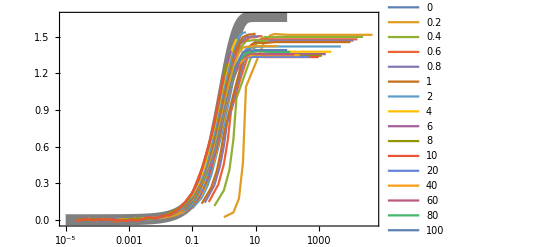

```mathematica
Show[
LogLinearPlot[(1-ⅇ^-x)/(4MKtime2),{x,10^-5,100}
,PlotStyle->{Thickness[0.02],Gray}
],
vplot2
,Frame->True
,PlotRange->All
]
```

```mathematica
ds2[Select[#["temperature"]==10000&]]⟦All,"Dxy"⟧
```

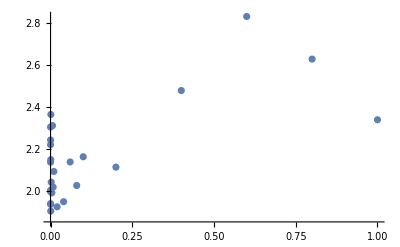

```mathematica
ListPlot[
ds2[Select[#["temperature"]==10000&]]⟦All,{"cmtratio","Dxy"}⟧
,PlotRange->All
]
```

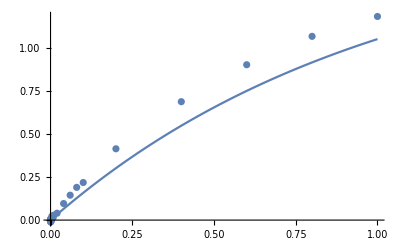

```mathematica
Show[
ListPlot[
ds2[Select[#["temperature"]==10000&]]⟦All,{"cmtratio","vmean"}⟧
,PlotRange->All
],
Plot[(1-ⅇ^-x)/(4MKtime2),{x,0,1}
]
]
```

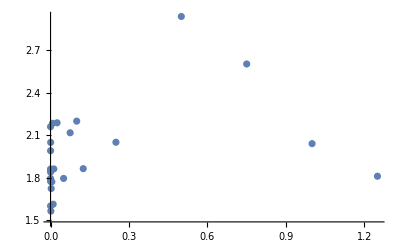

```mathematica
ListPlot[
ds2[Select[#["temperature"]==8000&]]⟦All,{"cmtratio","Dxy"}⟧
,PlotRange->All
]
```

OK, let’s figure out what T will give me the closest match to the σ I want. I’ll try to match it at μ=0.

```mathematica
μ02ds=ds2[Select[PossibleZeroQ[#["cmstrength"]]&]];
μ02ds=μ02ds[SortBy["temperature"]]
```

```mathematica
σ139/(gridunitD2 MKtime2)
```

0.781235 s

```mathematica
width2=height2=Quantity[0.2,"Centimeters"];
nx2=ny2=75;
dt2=Quantity[MKtime2,"Seconds"];
{dx2,dy2}={width2,height2}/{nx2,ny2}
```

{0.00266667 cm,0.00266667 cm}

```mathematica
{wormwidth2,wormlength2}=Quantity[{15,240},"Micrometers"]
```

{15 µm,240 µm}

```mathematica
wormsize2=(wormwidth2 wormlength2)/(dx2 dy2)
```

5.0625

```mathematica
σ139
```

5.55545×10^-6 cm^2/s

```mathematica
gridunitD2=(dx2 dy2)/dt2
```

0.0000474074 cm^2/s

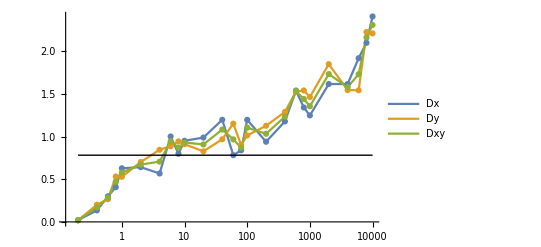
{0.2,10000,0.781235}
-Graphics-

```mathematica
Block[{is=400,ds=μ02ds,dfs={"Dx","Dy","Dxy"},data,mint,maxt,targetD},
ds=ds[Select[!PossibleZeroQ[#["temperature"]]&]];
targetD=(σ139/(dx2 dx2))Quantity[1,"Seconds"];
data=Table[
ds⟦All,{"temperature",d}⟧[Values]//Normal,
{d,dfs}
];
{mint,maxt}=MinMax[data⟦All,All,1⟧];
{
{mint,maxt,targetD},
ListLogLinearPlot[data
,PlotRange->All
,Joined->True
,Mesh->All
,ImageSize->is
,PlotLegends->dfs
,Epilog->{Line[{{Log[mint],targetD},{Log[maxt],targetD}}]}
]
}
]//Column
```

Looks like I want T≈6. I might use T=10 just to have a round number. It’s probably close enough, and I can always adjust MKtime if I want to.

```mathematica
μ02ds⟦All,{"temperature","Dxy"}⟧//Transpose
```

OK, now for the velocity, i.e. chemotaxis strength,

```mathematica
dx2
```

0.00266667 cm

Here I have an analytical expression that is accurate enough to go on with. In grid units, the velocity, for chemotaxis strength μ, field gradient ∇F, and temperature T, is

‖v‖=1/4(1-ⅇ^(-μ‖∇F‖/T))
≈(μ‖∇F‖)/(4T)

Strictly speaking, I know this only for the case of ∇F=(1,0). But I’m assuming (because I have no good alternative) that the chemotactic response is isotropic and that only the product μ∇F matters, i.e., the argument of the exponential is bilinear in μ and ∇F.

Suppose I have a potential field V in units of cm^2 s^-1. The gradient of this potential has units of velocity, specifically cm s^-1. What do I choose for μ? T is given—it was chosen to produce the right diffusion rate σ.) I’m going to assume the velocities are small.

∇F=∇Vdx
v=∇V(dt/dx)
≈(μ∇F)/(4T)
=(μ∇Vdx)/(4T)
∇V(dt/dx)≈(μ∇Vdx)/(4T)
1≈(μ dx^2)/(4Tdt)
μ≈(4Tdt)/dx^2

Here dt is the Metropolis kinetics time, e.g. 0.15 s for the case I’m working on, and dx is the grid spacing. This doesn’t seem right. It seems like dx ought to show up in the final computation of μ.

Well, let’s try an example. Suppose U_a changes from 0 to 25000 over a distance of 0.01 cm, which is plausible. Then V_U_a changes from 0 to -3×10^-5 over that distance. So the gradient is ‖∇V‖≈3×10^-3 cm/s.

```mathematica
Vu[
U_,
α_:1500,
β_:2σ139
]:=
-β Log[1+U/α];
```

```mathematica
{
"V"->Vu/@{0,25000},
"∇V"->Abs[Vu[25000]]/Quantity[0.01,"Centimeters"],
"∇F"->(QuantityMagnitude@Abs[Vu[25000]]/Quantity[0.01,"Centimeters"])dx2,
"v"->(Abs[Vu[25000]]/Quantity[0.01,"Centimeters"])(dt2/dx2),
"μ/T"->(4 dt2)/dx2^2,
"(μ ∇F)/T"->((4 dt2)/dx2^2)(Abs[Vu[25000]]/Quantity[0.01,"Centimeters"])dx2,
"(μ ∇F)/(4  T)"->((4 dt2)/(4 dx2^2))(Abs[Vu[25000]]/Quantity[0.01,"Centimeters"])dx2
}//Column
```

V→{0. cm^2/s,-0.0000319069 cm^2/s}
∇V→0.00319069 cm/s
∇F→8.50852×10^-6
v→0.179477
μ/T→84375. s/cm^2
(μ ∇F)/T→0.717906
(μ ∇F)/(4  T)→0.179477

Yup, looks like that works out.

## dt=0.05

```mathematica
μ01ds=ds1[Select[PossibleZeroQ[#["cmstrength"]]&]];
μ01ds=μ01ds[SortBy["temperature"]]
```

```mathematica
dt3=Quantity[0.05,"Seconds"]
```

0.05 s

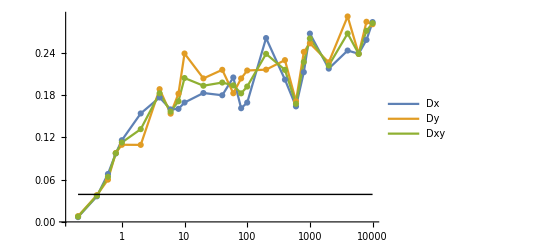
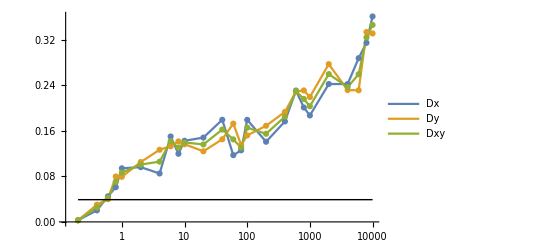
{0.2,10000,0.0390618}
-Graphics-
-Graphics-
{{{{0.2,0.00684214},{0.4,0.0363752},{0.6,0.0681142},{0.8,0.0972709},{1,0.116088},{2,0.154172},{4,0.176871},{6,0.159843},{8,0.160657},{10,0.169672},{20,0.183204},{40,0.179997},{60,0.205308},{80,0.161558},{100,0.16959},{200,0.261324},{400,0.202208},{600,0.164203},{800,0.212823},{1000,0.267672},{2000,0.217894},{4000,0.243589},{6000,0.239021},{8000,0.258732},{10000,0.284062}},{{0.2,0.00817876},{0.4,0.0380614},{0.6,0.0600807},{0.8,0.0979445},{1,0.109638},{2,0.109479},{4,0.188675},{6,0.153853},{8,0.182244},{10,0.239375},{20,0.203953},{40,0.216172},{60,0.182847},{80,0.20391},{100,0.215223},{200,0.21641},{400,0.229952},{600,0.171406},{800,0.241698},{1000,0.253822},{2000,0.226766},{4000,0.292021},{6000,0.238811},{8000,0.284503},{10000,0.280925}},{{0.2,0.00751045},{0.4,0.0372183},{0.6,0.0640975},{0.8,0.0976077},{1,0.112863},{2,0.131825},{4,0.182773},{6,0.156848},{8,0.17145},{10,0.204524},{20,0.193578},{40,0.198085},{60,0.194078},{80,0.182734},{100,0.192407},{200,0.238867},{400,0.21608},{600,0.167805},{800,0.22726},{1000,0.260747},{2000,0.22233},{4000,0.267805},{6000,0.238916},{8000,0.271617},{10000,0.282494}}},{{{0.2,0.00304257},{0.4,0.020259},{0.6,0.0449603},{0.8,0.060926},{1,0.0941652},{2,0.0961967},{4,0.0850713},{6,0.150077},{8,0.119695},{10,0.14255},{20,0.14813},{40,0.179439},{60,0.117218},{80,0.125769},{100,0.17933},{200,0.140799},{400,0.17653},{600,0.23075},{800,0.200992},{1000,0.187019},{2000,0.242201},{4000,0.242221},{6000,0.287654},{8000,0.314636},{10000,0.360919}},{{0.2,0.00266343},{0.4,0.030253},{0.6,0.0398233},{0.8,0.0798068},{1,0.0791562},{2,0.105167},{4,0.126692},{6,0.132855},{8,0.141443},{10,0.136437},{20,0.124031},{40,0.145128},{60,0.172696},{80,0.135051},{100,0.151939},{200,0.168871},{400,0.193256},{600,0.22885},{800,0.230961},{1000,0.219369},{2000,0.277141},{4000,0.231539},{6000,0.231221},{8000,0.333514},{10000,0.331074}},{{0.2,0.002853},{0.4,0.025256},{0.6,0.0423918},{0.8,0.0703664},{1,0.0866607},{2,0.100682},{4,0.105882},{6,0.141466},{8,0.130569},{10,0.139493},{20,0.136081},{40,0.162284},{60,0.144957},{80,0.13041},{100,0.165634},{200,0.154835},{400,0.184893},{600,0.2298},{800,0.215977},{1000,0.203194},{2000,0.259671},{4000,0.23688},{6000,0.259437},{8000,0.324075},{10000,0.345996}}}}

```mathematica
Block[{is=400,dss={μ01ds,μ02ds},dfs={"Dx","Dy","Dxy"},data,mint,maxt,targetD},
dss=Table[
ds[Select[!PossibleZeroQ[#["temperature"]]&]],
{ds,dss}
];
targetD=(σ139/(dx2 dx2))dt3;
data=Table[
ds⟦All,{"temperature",d}⟧[Values]//Normal,
{ds,dss},{d,dfs}
];
data⟦2,All,All,2⟧*=0.15;
{mint,maxt}=MinMax[data⟦All,All,All,1⟧];
{
{mint,maxt,targetD},
ListLogLinearPlot[data⟦1⟧
,PlotRange->All
,Joined->True
,Mesh->All
,ImageSize->is
,PlotLegends->dfs
,Epilog->{Line[{{Log[mint],targetD},{Log[maxt],targetD}}]}
],
ListLogLinearPlot[data⟦2⟧
,PlotRange->All
,Joined->True
,Mesh->All
,ImageSize->is
,PlotLegends->dfs
,Epilog->{Line[{{Log[mint],targetD},{Log[maxt],targetD}}]}
],
data
}
]//Column
```

## Equilibrium

Here’s another idea: perhaps I shouldn’t try to match the velocity, but merely the equilibrium. This is fairly straightforward. I know that at equilibrium, the is a Boltzmann equilibrium with temperature σ. But the Metropolis kinetics used for the cellular Potts model is based on a Boltzmann distribution. Thus I get the following simple answer for the chemotactic strength:

μ=T/σ

I tried that out, and it seems to work pretty well.